```mathematica
data = Import[NotebookDirectory[] <> "../data/btc future and reference rate/coingecko_future.csv"];
```

```mathematica
data[[1;;3]]
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
0 | 2021-02-03 | 37266.4 | 37790. | 0.0452987 | 0.0337738
1 | 2021-02-02 | 35615.9 | 36535. | 0.059664 | 0.0641463)

```mathematica
data = Import[NotebookDirectory[] <> "../data/cleaned_data/BBT_Tiingo.csv"];
```

```mathematica
data[[1;;3]]
```

( | Date | PX_LAST | contract_name | BTC Price | log return future | log return bitcoin
0 | 2021-05-27 20:00:00+00:00 | 38865. | BTCM1 Curncy | 38786.5 | 0.00658279 | 0.00753164
1 | 2021-05-26 20:00:00+00:00 | 38610. | BTCM1 Curncy | 38495.4 | 0.0326431 | 0.0311009)

```mathematica
data = Import[NotebookDirectory[] <> "../data/cleaned_data/BBT_future_CRIX.csv"];
```

```mathematica
data[[1;;3]]
```

( | Date | PX_LAST | contract_name | CRIX Price | log return future | log return CRIX
0 | 2021-05-27 20:00:00+00:00 | 38865. | BTCM1 Curncy | 4232.25 | 0.00658279 | 0.00557281
1 | 2021-05-26 20:00:00+00:00 | 38610. | BTCM1 Curncy | 4208.73 | 0.0326431 | 0.0540123)

```mathematica
data=data[[;;,{1,2,5,3,7,6}]];
```

```mathematica
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data]}];
```

```mathematica
Length[dates]
```

748

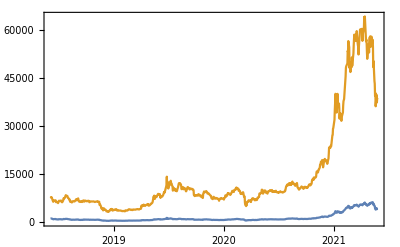

```mathematica
DateListPlot[{{dates,data[[2;;,3]]}ᵀ, {dates, data[[2;;,4]]}ᵀ},PlotRange->All]
```

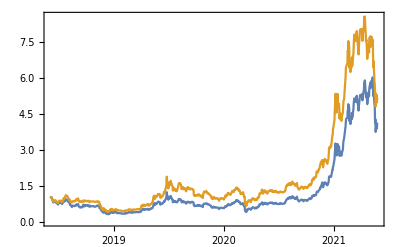

```mathematica
DateListPlot[{{dates,data[[2;;,3]]/data[[-1,3]]}ᵀ, {dates, data[[2;;,4]]/data[[-1,4]]}ᵀ},PlotRange->All]
```

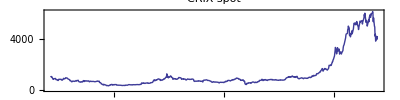

```mathematica
p1=DateListPlot[{dates,data[[2;;,3]]}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"CRIX spot",AspectRatio->1/4,PlotRange->Full]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_level_series.pdf", p1]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_level_series.pdf

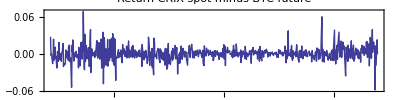

```mathematica
p1a=DateListPlot[{dates,Exp[data⟦2;;All,5⟧]-Exp[data⟦2;;All,6⟧]}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"Return CRIX spot minus BTC future",AspectRatio->1/4,PlotRange->Full]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_vs_future_series.pdf", p1a]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_vs_future_series.pdf

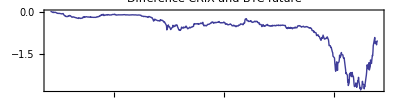

```mathematica
p2=DateListPlot[{dates,data[[2;;,3]]/data[[-1,3]]-data[[2;;,4]]/data[[-1,4]]}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"Difference CRIX and BTC future",PlotRange->All,AspectRatio->1/4]
```

```mathematica
(*Export[NotebookDirectory[] <> "../latex/_pics/btc_vs_future_series.pdf", p2]*)
```

```mathematica
(*p2=DateListPlot[{dates,data[[2;;,3]]-data[[2;;,4]]}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"Difference BTC spot and future",PlotRange->All,AspectRatio->1/4]*)
```

```mathematica
r=data⟦2;;All,5⟧;
f=data⟦2;;All,6⟧;
sr=Sort[r];
m=Mean[r];
s=StandardDeviation[r];
l=Length[r];
```

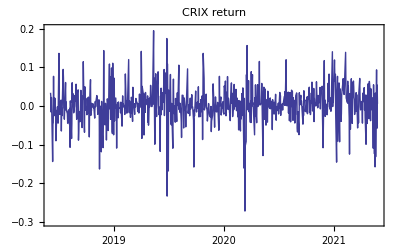

```mathematica
p3=DateListPlot[{dates,r}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"CRIX return",PlotRange->{-0.3, 0.2}]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_return_series.pdf", p3]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_return_series.pdf

```mathematica
extremes=Sort[Abs[r]]⟦-30;;All⟧;
pos=Flatten[Table[Position[Abs[r],extremes⟦k⟧],{k,1,Length[extremes]}]];
```

```mathematica
p3a=DateListPlot[Transpose[{dates⟦pos⟧,r⟦pos⟧}],PlotStyle->{Red,Thick},Joined->False];
```

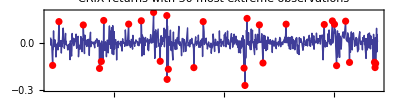

```mathematica
p3b=Show[p3,p3a, PlotLabel->"CRIX returns with 30 most extreme observations",AspectRatio->1/4]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_series.pdf", p3b]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_series.pdf

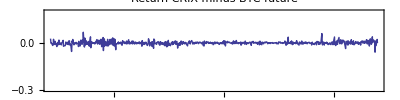

```mathematica
p1a=DateListPlot[{dates,Exp[data⟦2;;All,5⟧]-Exp[data⟦2;;All,6⟧]}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"Return CRIX minus BTC future",AspectRatio->1/4,PlotRange->{-0.3, 0.2}]
```

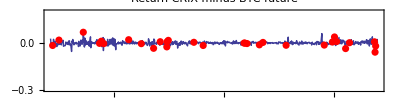

```mathematica
p1c=Show[p1a,DateListPlot[Transpose[{dates⟦pos⟧,(Exp[data⟦2;;All,5⟧]-Exp[data⟦2;;All,6⟧])⟦pos⟧}],PlotStyle->{Red,Thick},Joined->False]]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_vs_future_series.pdf", p1c]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_vs_future_series.pdf

```mathematica
NMaximize[{LogLikelihood[StudentTDistribution[ν], (r-m)/s],ν>2}, ν]
```

{-1035.37,{ν→8.5964}}

Generalized Pareto distribution

```mathematica
K=Ceiling[l 0.05];
u=-sr⟦K⟧
```

0.0748963

```mathematica
y=-sr⟦1;;K-1⟧-u;
```

```mathematica
Clear[ξ, β]
```

```mathematica
g[x_,β_,ξ_]:=1-(1+ξ x/β)^(-1/ξ)
```

```mathematica
NMaximize[{Total[Log[g[y,β,ξ]]],ξ>0&& β>0},{β,ξ}]
```

{-1.11022×10^-16,{β→8.39068×10^-7,ξ→0.191088}}

```mathematica
1/0.20327
```

4.91957

```mathematica
1/0.191088
```

5.23319

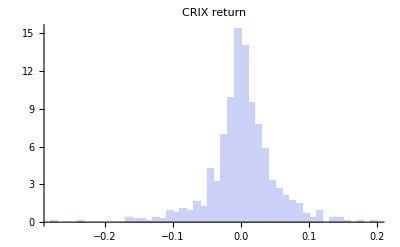

```mathematica
p4=Histogram[data[[2;;,5]],Automatic, "PDF", PlotTheme->"Classic", PlotLabel->"CRIX return",PlotRange->All]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_hist.pdf", p4]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_hist.pdf

See gretl for summary statistics

```mathematica
t=Table[{InverseCDF[NormalDistribution[m,s],(k-0.5)/l],sr[[k]]}, {k,1,l}];
```

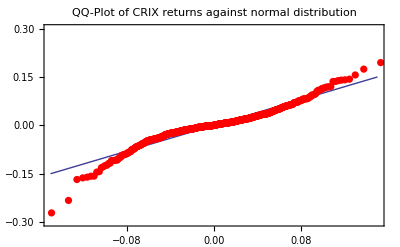

```mathematica
p5=Show[
Plot[x, {x,-0.15, 0.15},PlotTheme->"Classic",PlotRange->{-0.3,0.3}, Frame->True,PlotLabel->"QQ-Plot of CRIX returns against normal distribution"],
ListPlot[t, PlotTheme->"Classic", PlotStyle->{Red, PointSize[0.013]},PlotRange->All]
]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_qq.pdf", p5]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_qq.pdf

Outliers are 3/2 times beyond the interquartile range; far outliers are beyond 3 times  the interquartile range.

```mathematica
Clear[o]
```

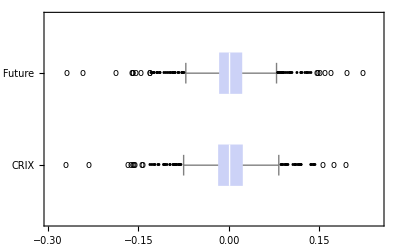

```mathematica
p6=BoxWhiskerChart[{r,f},{{"Outliers", "•"},{"FarOutliers", o}},PlotTheme->"Classic",  ChartLabels->{"CRIX", "BTC Future"},BarOrigin->Left]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_future_box.pdf", p6]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_future_box.pdf

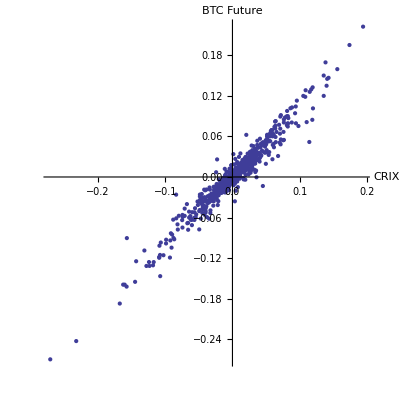

```mathematica
p7=ListPlot[{r,f}ᵀ,PlotTheme->"Classic",AxesLabel->{"CRIX", "BTC Future"},PlotRange->All, AspectRatio->1]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_future_scatter.pdf", p7]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_future_scatter.pdf

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
usim=hatF[r];
vsim=hatF[f];
```

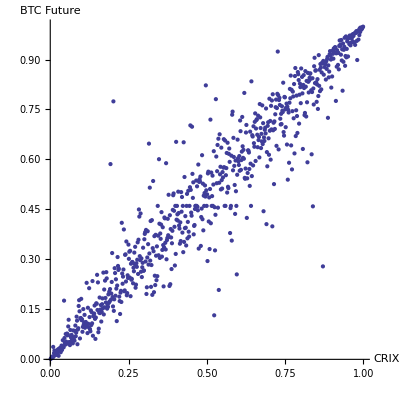

```mathematica
p8=ListPlot[{usim,vsim}ᵀ,PlotTheme->"Classic",AxesLabel->{"CRIX", "BTC Future"},PlotRange->All, AspectRatio->1]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_future_copula_scatter.pdf", p8]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_future_copula_scatter.pdf

## Copula scatterplots

```mathematica
Clear[u,v,ρ,p]
```

```mathematica
sp[dist_]:=12 NIntegrate[CDF[dist,{u,v}], {u,0,1}, {v,0,1}]-3
```

Gaussian copula / Spearman’s rho

```mathematica
sol=Solve[ 6/Pi ArcSin[1/2 ρ]==0.75,ρ]
```

{{ρ→0.765367}}

```mathematica
gaussian = CopulaDistribution[{"Binormal", ρ/.sol[[1]]}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[gaussian]
```

0.75

```mathematica
Plot3D[PDF[gaussian, {u,v}], {u,0,1}, {v,0,1},PlotTheme->"Classic"]
```

-Graphics3D-

```mathematica
r1=RandomVariate[gaussian, 1000];
```

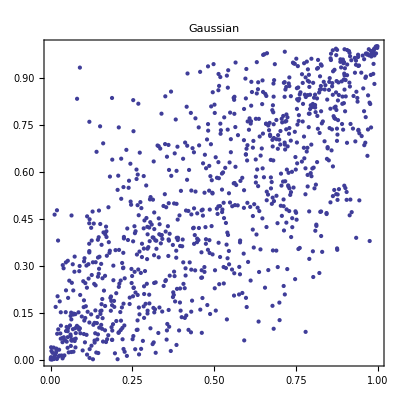

```mathematica
p1=ListPlot[r1,PlotTheme->"Classic", PlotStyle->Thick,Frame->True,PlotLabel->"Gaussian", AspectRatio->1]
```

Multivariate T

```mathematica
ρ=0.77025;StudentT=CopulaDistribution[{"MultivariateT", {{1,ρ}, {ρ,1}}, 10}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[StudentT]
```

0.749847

```mathematica
r2=RandomVariate[StudentT, 1000];
```

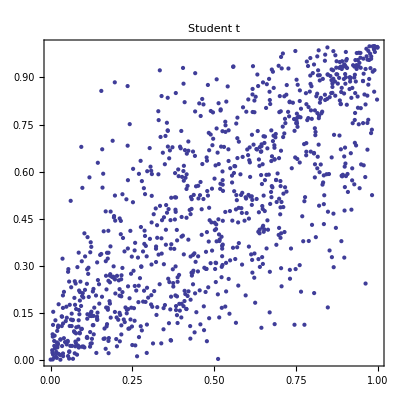

```mathematica
p2=ListPlot[r2,PlotTheme->"Classic", PlotStyle->Thick,Frame->True,PlotLabel->"Student t", AspectRatio->1]
```

Clayton

```mathematica
c=0.3875;
clayton = CopulaDistribution[{"Clayton", c}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[clayton]
```

0.75009

```mathematica
r3=RandomVariate[clayton, 1000];
```

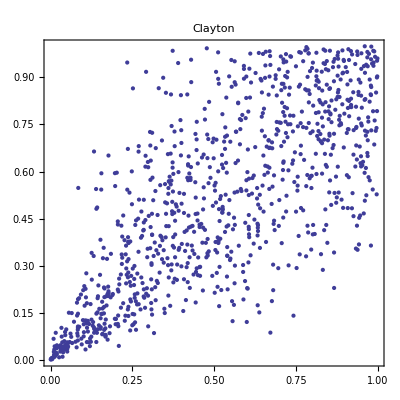

```mathematica
p3=ListPlot[r3,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Clayton", AspectRatio->1]
```

Frank

```mathematica
α=0.001199;
frank = CopulaDistribution[{"Frank", α}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[frank]
```

0.750022

```mathematica
r4=RandomVariate[frank, 1000];
```

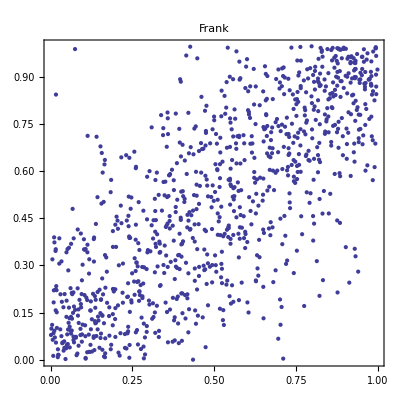

```mathematica
p4=ListPlot[r4,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Frank", AspectRatio->1]
```

Gumbel

```mathematica
α=2.2855;
gumbel=CopulaDistribution[{"GumbelHougaard", α}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[gumbel]
```

0.750056

```mathematica
r5=RandomVariate[gumbel, 1000];
```

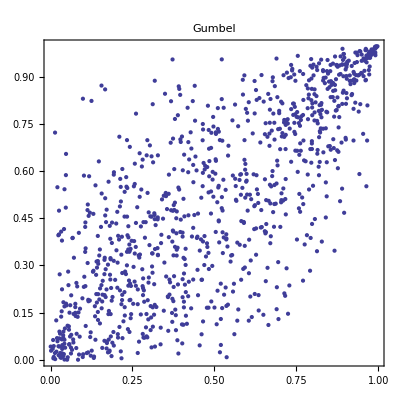

```mathematica
p5=ListPlot[r5,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Gumbel", AspectRatio->1]
```

Plackett
From Nelsen, p.99/100

From Nelsen, p. 171:

```mathematica
Clear[θ]
NSolve[0.75==(θ+1)/(θ-1)-(2 θ Log[θ])/(θ-1)^2,θ]
```

NSolve[0.75==(θ+1)/(θ-1)-(2 θ log(θ))/(θ-1)^2,θ]

```mathematica
sol=NMinimize[{(0.75-((θ+1)/(θ-1)-(2 θ Log[θ])/(θ-1)^2))^2,θ>0},{θ,15,20}]
```

{6.48932×10^-16,{θ→17.1395}}

```mathematica
θ=θ/.sol[[2]];
u=RandomVariate[UniformDistribution[],1000];
t=RandomVariate[UniformDistribution[],1000];
```

```mathematica
a=t (1-t);
b=θ+a (θ-1)^2;
c=2 a (u θ^2+1-u)+θ (1-2 a);
d=√θ √(θ+4 a u (1-u) (1-θ)^2);
v=(c-(1-2t )d)/(2 b);
```

```mathematica
r6 = {u,v}ᵀ;
```

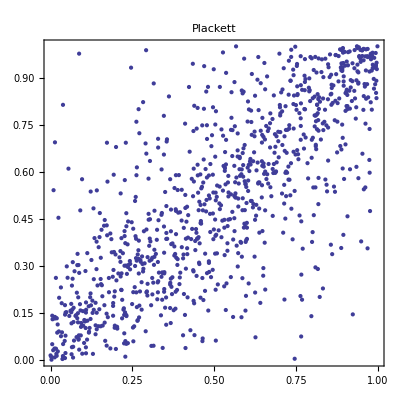

```mathematica
p6=ListPlot[r6,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Plackett", AspectRatio->1]
```

NIG factor model

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

```mathematica
α=1.5;
β=0.1;
Clear[δ]
```

Spearman Rho approximation of Gaussian

```mathematica
sol=NSolve[(6 ArcSin[δ/(2 δs[α,β])])/π==0.75, δ]
```

{{δ→1.14041}}

```mathematica
δ=δ/.sol⟦1⟧;
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
```

```mathematica
Y=RandomVariate[NormalDistribution[],{3,1000}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], 1000];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], 1000];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], 1000];
```

```mathematica
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
```

```mathematica
SpearmanRho[X1,X2]
```

0.720727

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Timing[
usim = hatF[X1];
vsim = hatF[X2];
]
```

{0.039678,Null}

```mathematica
r7 = {usim,vsim}ᵀ;
```

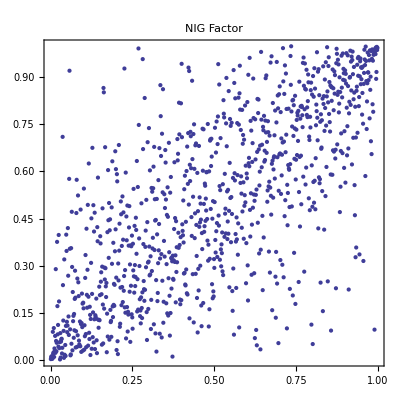

```mathematica
p7=ListPlot[r7,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"NIG Factor", AspectRatio->1]
```

Mixture copula

```mathematica
Clear[ρ,p]
```

```mathematica
p=0.8;
sol=Solve[ p 6/Pi ArcSin[1/2 ρ]==0.75,ρ]
```

{{ρ→0.942793}}

```mathematica
ρ=ρ/.sol[[1]]
```

0.942793

```mathematica
mixture = p CopulaDistribution[{"Binormal", ρ}, {UniformDistribution[], UniformDistribution[]}] + (1-p) CopulaDistribution["Product", {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[CopulaDistribution["Product", {UniformDistribution[], UniformDistribution[]}]]
```

-8.88178×10^-16

```mathematica
p sp[CopulaDistribution[{"Binormal", ρ}, {UniformDistribution[], UniformDistribution[]}]]
```

0.75

```mathematica
Plot3D[p PDF[CopulaDistribution[{"Binormal", ρ}, {UniformDistribution[], UniformDistribution[]}],{u,v}]+ (1-p) PDF[CopulaDistribution["Product", {UniformDistribution[], UniformDistribution[]}],{u,v}], {u,0,1}, {v,0,1}]
```

-Graphics3D-

```mathematica
X=RandomVariate[NormalDistribution[],1000];
Z=RandomVariate[NormalDistribution[],1000];
W=RandomVariate[UniformDistribution[],1000];
```

```mathematica
Y=ConstantArray[0, 1000];
```

```mathematica
Table[If[W⟦k⟧≤p,Y⟦k⟧=ρ X⟦k⟧+√(1-ρ^2) Z⟦k⟧,Y⟦k⟧=Z⟦k⟧],{k,1,1000}];
```

```mathematica
Timing[
usim = hatF[X];
vsim = hatF[Y];
]
```

{0.040209,Null}

```mathematica
r8 = {usim,vsim}ᵀ;
```

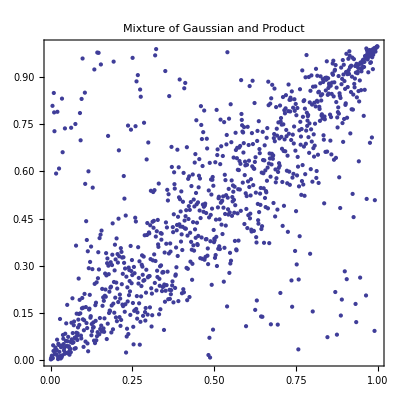

```mathematica
p8=ListPlot[r8,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Mixture of Gaussian and Product", AspectRatio->1]
```

```mathematica
(*p CDF[CopulaDistribution[{"Binormal", ρ}, {UniformDistribution[], UniformDistribution[]}],{u,v}]+ (1-p)CDF[CopulaDistribution["Product", {UniformDistribution[], UniformDistribution[]}],{u,v}]/.{u->.85, v->.65}*)
```

```mathematica
Length[Select[{usim, vsim}ᵀ, #1[[1]]<=0.85 && #1[[2]]≤0.65&]]/1000.
```

0.63

```mathematica
Grid[{{p1, p2, p3, p4}, {},{p5, p6, p7, p8}}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/copulas_scatterplots.pdf", %]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/copulas_scatterplots.pdf

## h Parameters

```mathematica
methods={"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"};
```

```mathematica
(*hParams=Import[NotebookDirectory[] <> "../results/BBT_Tiingo/MM/OHR.csv"];*)
```

```mathematica
hParams=Import[NotebookDirectory[] <> "../results/BBT_future_CRIX/MM/OHR.csv"];
```

```mathematica
(*hParams=Import[NotebookDirectory[] <> "../results/coingecko_future_v3/MM/OHR.csv"];*)
```

```mathematica
Dimensions[hParams]
```

{4225,5}

```mathematica
dates={};
For[k=0, k≤87, k++,
d=Import[NotebookDirectory[] <> "../processed_data/BBT_future_CRIX/train/"<> ToString[k] <> ".csv"];
AppendTo[dates,DateList[{StringSplit[d⟦2,2⟧][[1]], {"Year", "Month", "Day"}}]];
]
```

```mathematica
hParams[[1;;10]]
```

( | file | risk measure | OHR | copula
0 | 83.csv | Variance | 0.883691 | Gaussian
1 | 83.csv | ERM k=10 | 0.891211 | Gaussian
2 | 83.csv | ES q=0.01 | 0.832227 | Gaussian
3 | 83.csv | ES q=0.05 | 0.890039 | Gaussian
4 | 83.csv | VaR q=0.01 | 0.903125 | Gaussian
5 | 83.csv | VaR q=0.05 | 0.934668 | Gaussian
6 | 68.csv | Variance | 0.878906 | Gaussian
7 | 68.csv | ERM k=10 | 0.88584 | Gaussian
8 | 68.csv | ES q=0.01 | 0.872559 | Gaussian)

```mathematica
copulas=Union[hParams[[2;;,5]], {}];
measures=Union[hParams[[2;;,3]], {}];
```

```mathematica
copulas
```

{Clayton,Frank,Gaussian,Gauss Mix Indep,Gumbel,Plackett,t_Copula,t_Copula_Capped}

```mathematica
measures
```

{ERM k=10,ES q=0.01,ES q=0.05,Variance,VaR q=0.01,VaR q=0.05}

```mathematica
methods
```

{Variance,VaR 99%,VaR 95%,ES 99%,ES 95%,Spectral 10}

```mathematica
measures={measures⟦4⟧,measures⟦5⟧,measures⟦6⟧,measures⟦2⟧,measures⟦3⟧,measures⟦1⟧}
```

{Variance,VaR q=0.01,VaR q=0.05,ES q=0.01,ES q=0.05,ERM k=10}

```mathematica
hGaussian=Select[hParams, #1[[5]]=="Gaussian"&];
```

```mathematica
hGaussian[[1;;10]]
```

(0 | 83.csv | Variance | 0.883691 | Gaussian
1 | 83.csv | ERM k=10 | 0.891211 | Gaussian
2 | 83.csv | ES q=0.01 | 0.832227 | Gaussian
3 | 83.csv | ES q=0.05 | 0.890039 | Gaussian
4 | 83.csv | VaR q=0.01 | 0.903125 | Gaussian
5 | 83.csv | VaR q=0.05 | 0.934668 | Gaussian
6 | 68.csv | Variance | 0.878906 | Gaussian
7 | 68.csv | ERM k=10 | 0.88584 | Gaussian
8 | 68.csv | ES q=0.01 | 0.872559 | Gaussian
9 | 68.csv | ES q=0.05 | 0.886523 | Gaussian)

```mathematica
p={};
hFull={};
For[j=1, j≤Length[copulas], j++,
h={};
For[k=1, k≤Length[measures], k++,
htmp1=Select[hParams,#1⟦5⟧==copulas⟦j⟧&];
htmp=Select[htmp1,#1⟦3⟧==measures⟦k⟧&];
o=Ordering[ToExpression[StringReplace[htmp⟦1;;All,2⟧,".csv"->""]]];
AppendTo[h,htmp⟦o,4⟧];
];
AppendTo[p,DateListPlot[Table[{dates,h⟦k⟧}ᵀ,{k,1,Length[h]}],(*PlotLegends->measures,*)PlotLabel->copulas⟦j⟧,PlotRange->{0,1.3}]];
AppendTo[hFull, h];
]
```

Add NIG factor

```mathematica
hvec={};
For[j=0, j≤87, j++,
AppendTo[hvec, Import[NotebookDirectory[] <> "data/" <> ToString[j] <> "_h.csv"]];
(* order of risk measures: variance, VaR99, VaR95, ES99, ES95, Spectral10 *)
]
```

```mathematica
AppendTo[copulas, "NIG Factor"];
```

```mathematica
h={};
AppendTo[h,hvec[[;;,2]]];
AppendTo[h,hvec[[;;,3]]];
AppendTo[h,hvec[[;;,4]]];
AppendTo[h,hvec[[;;,5]]];
AppendTo[h,hvec[[;;,6]]];
AppendTo[h,hvec[[;;,7]]];
```

```mathematica
AppendTo[hFull,h[[;;,;;,1]]];
```

```mathematica
AppendTo[p,DateListPlot[Table[Transpose[{dates,h⟦k⟧}],{k,1,Length[h]}],(*PlotLegends->measures,*)PlotLabel->"NIG Factor",PlotRange->{0,1.3}]];
```

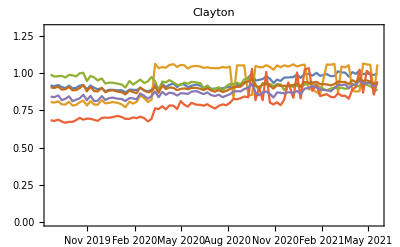
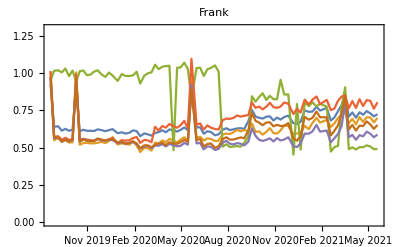
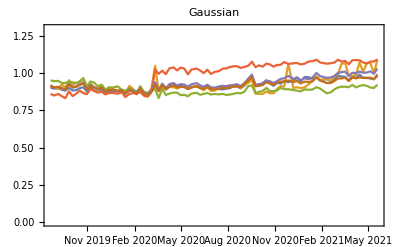
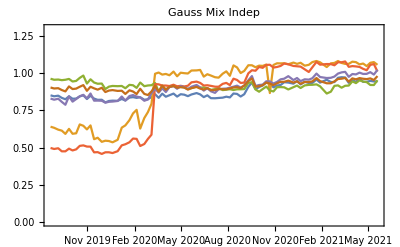
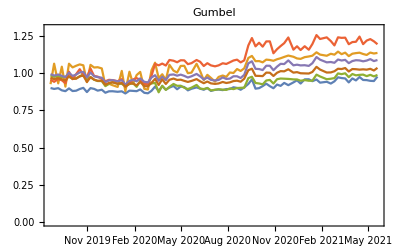
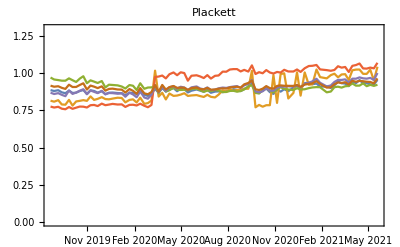
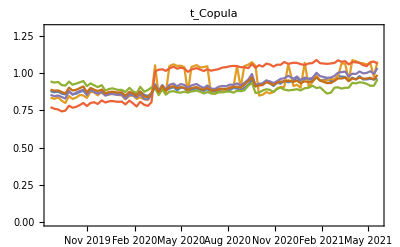
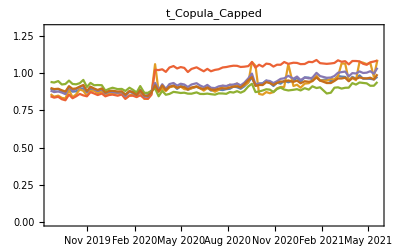

```mathematica
p
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/hParams_Legend.pdf",LineLegend[ColorData[97, "ColorList"],methods, LegendLayout->"Row"]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/hParams_Legend.pdf

```mathematica
Export[NotebookDirectory[]<> "../latex/_pics/hParams.pdf", Grid[{{p⟦3⟧,p⟦7⟧,p⟦1⟧,p⟦2⟧},{p⟦5⟧,p⟦6⟧,p⟦9⟧,p⟦4⟧}}]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/hParams.pdf

## P&L

```mathematica
Dimensions[hFull]
```

{9,6,88}

```mathematica
Dimensions[hFull⟦1⟧]
```

{6,88}

h’s were generated with 30 days test in mind. For 100 days test, we need to discard data until 10 Sep 2020. 
Starting index:

```mathematica
dates⟦20⟧
```

{2020,12,29,0,0,0.}

```mathematica
htmp=hFull[[9]];
```

```mathematica
htmp[[;;,20]]
```

{0.94351,0.90937,0.951207,0.903872,0.955393,0.976341}

### In-sample P&L

```mathematica
methods
measures
copulas
```

{Variance,VaR 99%,VaR 95%,ES 99%,ES 95%,Spectral 10}

{Variance,VaR q=0.01,VaR q=0.05,ES q=0.01,ES q=0.05,ERM k=10}

{Clayton,Frank,Gaussian,Gauss Mix Indep,Gumbel,Plackett,t_Copula,t_Copula_Capped,NIG Factor}

```mathematica
For[ii=1, ii≤ Length[copulas], ii++,
htmp=hFull[[ii]];
For[kk=0, kk≤67, kk++,
data = (* in sample *)
Import[NotebookDirectory[] <> "../processed_data/BBT_future_CRIX/train/" <> ToString[20+kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,6⟧];
brr=Reverse[data⟦2;;All,7⟧];
(* hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"]; *)
hvec=htmp[[;;,20+kk]];
PLdyn={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLstat={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PLdyn, PLbrr];
AppendTo[PLstat,Flatten[{"unhedged",Exp[Accumulate[rbrr]]}]];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc = Exp[btc]-1;
rbtc = Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PLdyn,PLbtc];
AppendTo[PLstat,Flatten[{"future", Exp[Accumulate[rbtc]]}]];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=1, jj≤Length[hvec],jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0; (* dynamic hedge; every day starts with h units of future *)
rh=Log[(1+PLh)];
PLs=Exp[Accumulate[rh]];
PrependTo[PLh, methods⟦jj⟧];
AppendTo[PLdyn, PLh];
PrependTo[PLs, methods⟦jj⟧];
AppendTo[PLstat, PLs];
PrependTo[rh, methods⟦jj⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data_PL/" <> ToString[kk] <> "_"<> copulas[[ii]] <> "_PL_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data_PL/" <> ToString[kk] <> "_"<>copulas[[ii]]<> "_PLr_insample.csv",PLrᵀ]
]
]
```

### Out-of-sample P&L

We use the h’s calibrated every 5 days on 300 days of history and build out-of-sample data sets of size 100

```mathematica
For[ii=1, ii≤  Length[copulas], ii++,
htmp=hFull⟦ii⟧;
For[kk=0, kk≤ 67, kk++,
data = (* out-of-sample *)
Import[NotebookDirectory[] <> "../processed_data/BBT_future_CRIX/test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,6⟧];
brr=Reverse[data⟦2;;All,7⟧];
(*  hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];*)
hvec=htmp[[;;,20+kk]];
PLdyn={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};PLstat={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PLdyn, PLbrr];
AppendTo[PLstat,Flatten[{"unhedged",Exp[Accumulate[rbrr]]}]];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PLdyn,PLbtc];
AppendTo[PLstat,Flatten[{"future", Exp[Accumulate[rbtc]]}]];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=1, jj≤Length[hvec],jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PLs=Exp[Accumulate[rh]];
PrependTo[PLh, methods⟦jj⟧];
AppendTo[PLdyn, PLh];
PrependTo[PLs, methods⟦jj⟧];
AppendTo[PLstat, PLs];
PrependTo[rh, methods⟦jj⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data_PL/" <> ToString[kk] <> "_"<> copulas[[ii]] <> "_PL_outsample.csv",PLdynᵀ];
Export[NotebookDirectory[] <> "data_PL/" <> ToString[kk] <> "_"<>copulas[[ii]]<> "_PLr_outsample.csv",PLrᵀ]
]
]
```

### Out-of-sample P&L (5 days)

We use the h’s calibrated every 5 days on 300 days of history and build out-of-sample data sets of size 5

```mathematica
For[ii=1, ii≤ Length[copulas], ii++,
htmp=hFull⟦ii⟧;
For[kk=0, kk≤ 87, kk++,
data = (* out-of-sample *)
Import[NotebookDirectory[] <> "../processed_data/BBT_future_CRIX/test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,6⟧];
brr=Reverse[data[[2;;All,7]]];
(*  hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];*)
hvec=htmp⟦1;;All,1+kk⟧;
PLdyn={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};PLstat={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PLdyn, PLbrr];
AppendTo[PLstat,Flatten[{"unhedged",Exp[Accumulate[rbrr]]}]];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PLdyn,PLbtc];
AppendTo[PLstat,Flatten[{"future", Exp[Accumulate[rbtc]]}]];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=1, jj≤Length[hvec],jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PLs=Exp[Accumulate[rh]];
PrependTo[PLh, methods⟦jj⟧];
AppendTo[PLdyn, PLh];
PrependTo[PLs, methods⟦jj⟧];
AppendTo[PLstat, PLs];
PrependTo[rh, methods⟦jj⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data_PL_5Days/" <> ToString[kk] <> "_"<> copulas[[ii]] <> "_PL_outsample.csv",PLdynᵀ];
Export[NotebookDirectory[] <> "data_PL_5Days/" <> ToString[kk] <> "_"<>copulas[[ii]]<> "_PLr_outsample.csv",PLrᵀ]
]
]
```

## P&L Plots

Which kind of P&L to look at? 
- 5 days (this would be daily return P&L, recalibrated as often as possible)
- 100 days (this would be the P&L of a static hedge, so only final P&L counts)

In-sample
This doesn’t make much sense as the samples are overlapping, so it’s not clear which h to associate with which time period in-sample.

#### Out-of-sample (static)

This uses a out-of-sample period of 100 days.

```mathematica
copulas={"Clayton","Frank","Gaussian","Gauss Mix Indep","Gumbel","Plackett","t_Copula","t_Copula_Capped","NIG Factor"};
```

```mathematica
measures={"ERM k=10","ES q=0.01","ES q=0.05","Variance","VaR q=0.01","VaR q=0.05"};
```

```mathematica
methods={"Variance","VaR 99%","VaR 95%","ES 99%","ES 95%","Spectral 10"};
```

```mathematica
dFull={};
For[ii=1, ii≤Length[copulas],ii++,
d={};
For[kk=0, kk≤67, kk++,
d1=Import[NotebookDirectory[] <> "data_PL/" <> ToString[kk] <> "_" <> copulas[[ii]]<> "_PLr_outsample.csv"];
If[kk==0,
d=Append[{d1[[1,2;;]]}, Exp[Total[d1[[2;;,2;;]]]]],
d=AppendTo[d,Exp[Total[d1[[2;;,2;;]]]]]
];
];
AppendTo[dFull, d];
]
```

```mathematica
Dimensions[d1]
```

{6,9}

```mathematica
Dimensions[dFull]
```

{9,69,8}

```mathematica
measures=dFull[[9,1,3;;]]
```

{Variance,VaR 99%,VaR 95%,ES 99%,ES 95%,Spectral 10}

```mathematica
dFull[[2,1;;10]]//TableForm
```

unhedged | future | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
0.964692 | 0.963197 | 0.996595 | 0.99303 | 0.998349 | 0.998978 | 0.991112 | 0.995124
0.814795 | 0.832216 | 0.928625 | 0.915491 | 0.896765 | 0.939182 | 0.903957 | 0.912043
0.909923 | 0.858445 | 1.00617 | 0.996745 | 1.02588 | 1.02108 | 0.983296 | 0.989557
1.10015 | 1.06546 | 1.05419 | 1.0595 | 1.06927 | 1.04969 | 1.06526 | 1.06152
1.02117 | 0.998964 | 1.02229 | 1.02236 | 1.022 | 1.02215 | 1.0224 | 1.02235
0.870438 | 0.825208 | 0.997484 | 0.987057 | 1.02612 | 1.01595 | 0.96939 | 0.986474
1.12648 | 1.09839 | 1.0566 | 1.06388 | 1.03008 | 1.04787 | 1.07067 | 1.06093
1.00319 | 0.97364 | 1.02238 | 1.01955 | 1.02561 | 1.02409 | 1.01872 | 1.0211
1.12479 | 1.14741 | 1.02456 | 1.0367 | 1.00425 | 1.01174 | 1.04475 | 1.03016

dsv: downside semi variance

```mathematica
rmse={};
dsv={};
For[ii=1, ii≤Length[copulas],ii++,
AppendTo[rmse,Table[RootMeanSquare[dFull[[ii,2;;,kk]]-1], {kk,1,8}]];
AppendTo[dsv, Table[RootMeanSquare[Min[#-1,0]&/@dFull[[ii,2;;,kk]]], {kk,1,8}]];
]
```

```mathematica
Min[#-1,0]&/@dFull[[1,2;;,1]]
```

{-0.0353078,-0.185205,-0.0900773,0,0,-0.129562,0,0,0,-0.0912907,-0.00754549,0,0,-0.0702841,0,0,0,-0.0849255,-0.00106145,0,0,0,-0.00117592,0,0,0,0,0,0,0,0,0,0,-0.041827,0,-0.112643,0,-0.0190979,0,-0.0144603,0,0,0,0,0,-0.0481612,0,-0.032708,0,0,-0.00625212,-0.0674871,0,0,0,-0.0252964,0,0,0,0,-0.352181,0,-0.080617,-0.0846757,0,0,0,0}

```mathematica
dFull[[1,2;;,1]]-1
```

{-0.0353078,-0.185205,-0.0900773,0.100149,0.0211693,-0.129562,0.126477,0.00319218,0.124794,-0.0912907,-0.00754549,0.184909,0.00251682,-0.0702841,0.164524,0.407663,0.0326363,-0.0849255,-0.00106145,0.38916,0.157085,0.159905,-0.00117592,0.121052,0.00405461,0.103438,0.0741527,0.0995382,0.00994504,0.124167,0.0591579,0.0190884,0.00511782,-0.041827,0.0597163,-0.112643,0.0102619,-0.0190979,0.00861451,-0.0144603,0.0761102,0.212365,0.011148,0.00716101,0.0132774,-0.0481612,0.0176462,-0.032708,0.0120567,0.0419132,-0.00625212,-0.0674871,0.114528,0.162487,0.0642983,-0.0252964,0.0878278,0.0244288,0.0586176,0.0324216,-0.352181,0.0170901,-0.080617,-0.0846757,0.105151,0.0562889,0.0765556,0.00202142}

```mathematica
rrmse={};
rdsv={};
For[ii=1, ii≤Length[copulas],ii++,
AppendTo[rrmse,Table[RootMeanSquare[dFull[[ii,2;;,kk]]-1]/rmse[[1,1]], {kk,3,8}]];
AppendTo[rdsv, Table[RootMeanSquare[Min[#-1,0]&/@dFull[[ii,2;;,kk]]]/dsv[[1,1]], {kk,3,8}]];

]
```

```mathematica
rmseTable=Prepend[Prepend[rmse,dFull[[1,1]]]ᵀ,Flatten[Join[{""},copulas]]]//TableForm
```

| Clayton | Frank | Gaussian | Gauss Mix Indep | Gumbel | Plackett | t_Copula | t_Copula_Capped | NIG Factor
unhedged | 0.115607 | 0.115607 | 0.115607 | 0.115607 | 0.115607 | 0.115607 | 0.115607 | 0.115607 | 0.115607
future | 0.116793 | 0.116793 | 0.116793 | 0.116793 | 0.116793 | 0.116793 | 0.116793 | 0.116793 | 0.116793
Variance | 0.0195667 | 0.0423284 | 0.0199479 | 0.022402 | 0.0202042 | 0.0208634 | 0.0208303 | 0.0202018 | 0.0194027
VaR 99% | 0.0267683 | 0.0492979 | 0.0192279 | 0.0301546 | 0.0213228 | 0.0242122 | 0.0206605 | 0.0202117 | 0.0200179
VaR 95% | 0.0181213 | 0.0402421 | 0.020235 | 0.0192863 | 0.0189854 | 0.0196353 | 0.0200252 | 0.0201664 | 0.0189415
ES 99% | 0.0300915 | 0.0412386 | 0.0220272 | 0.0366904 | 0.025703 | 0.0238933 | 0.0246306 | 0.0226624 | 0.0223815
ES 95% | 0.0223255 | 0.0533481 | 0.0194982 | 0.0214306 | 0.0197091 | 0.0204698 | 0.0204509 | 0.0198436 | 0.0193241
Spectral 10 | 0.0198746 | 0.0494488 | 0.0196247 | 0.0198783 | 0.0189383 | 0.0196804 | 0.0200754 | 0.0198181 | 0.0191441

```mathematica
dsvTable=Prepend[Prepend[dsv,dFull[[1,1]]]ᵀ,Flatten[Join[{""},copulas]]]//TableForm
```

| Clayton | Frank | Gaussian | Gauss Mix Indep | Gumbel | Plackett | t_Copula | t_Copula_Capped | NIG Factor
unhedged | 0.0596964 | 0.0596964 | 0.0596964 | 0.0596964 | 0.0596964 | 0.0596964 | 0.0596964 | 0.0596964 | 0.0596964
future | 0.0631509 | 0.0631509 | 0.0631509 | 0.0631509 | 0.0631509 | 0.0631509 | 0.0631509 | 0.0631509 | 0.0631509
Variance | 0.00773707 | 0.022626 | 0.00826656 | 0.0103656 | 0.0085317 | 0.00925635 | 0.0090555 | 0.00851877 | 0.00776117
VaR 99% | 0.0132944 | 0.0272788 | 0.00791378 | 0.0191386 | 0.00988718 | 0.0125414 | 0.0107122 | 0.00912805 | 0.00819444
VaR 95% | 0.00733701 | 0.016643 | 0.00811395 | 0.00743683 | 0.00693584 | 0.00763438 | 0.0081075 | 0.0081884 | 0.00743699
ES 99% | 0.0171589 | 0.024255 | 0.0108459 | 0.0247797 | 0.0146074 | 0.0136048 | 0.0140397 | 0.0116488 | 0.0131037
ES 95% | 0.0113306 | 0.0276878 | 0.00765496 | 0.0101739 | 0.00812003 | 0.00918515 | 0.00890496 | 0.00812256 | 0.00788886
Spectral 10 | 0.00853796 | 0.0266613 | 0.00788997 | 0.00818591 | 0.00711436 | 0.00809322 | 0.00840969 | 0.0081285 | 0.00727293

```mathematica
o={3,7,1,2,5,6,9,4}; (* ordering *)
```

```mathematica
copulas[[o]]
```

{Gaussian,t_Copula,Clayton,Frank,Gumbel,Plackett,NIG Factor,Gauss Mix Indep}

```mathematica
rrmseTable=Prepend[Prepend[rrmse[[o]],dFull[[1,1,3;;]]]ᵀ,Flatten[Join[{""},copulas[[o]]]]]//TableForm
```

| Gaussian | t_Copula | Clayton | Frank | Gumbel | Plackett | NIG Factor | Gauss Mix Indep
Variance | 0.17255 | 0.180183 | 0.169252 | 0.366141 | 0.174767 | 0.180469 | 0.167834 | 0.193778
VaR 99% | 0.166321 | 0.178713 | 0.231546 | 0.426427 | 0.184442 | 0.209436 | 0.173155 | 0.260838
VaR 95% | 0.175033 | 0.173218 | 0.156749 | 0.348095 | 0.164224 | 0.169845 | 0.163844 | 0.166827
ES 99% | 0.190535 | 0.213055 | 0.260292 | 0.356714 | 0.222332 | 0.206678 | 0.1936 | 0.317372
ES 95% | 0.16866 | 0.1769 | 0.193116 | 0.461462 | 0.170484 | 0.177064 | 0.167154 | 0.185375
Spectral 10 | 0.169754 | 0.173653 | 0.171916 | 0.427733 | 0.163816 | 0.170236 | 0.165597 | 0.171948

```mathematica
rdsvTable=Prepend[Prepend[rdsv[[o]],dFull[[1,1,3;;]]]ᵀ,Flatten[Join[{""},copulas[[o]]]]]//TableForm
```

| Gaussian | t_Copula | Clayton | Frank | Gumbel | Plackett | NIG Factor | Gauss Mix Indep
Variance | 0.138477 | 0.151693 | 0.129607 | 0.379017 | 0.142918 | 0.155057 | 0.130011 | 0.173639
VaR 99% | 0.132567 | 0.179445 | 0.2227 | 0.456959 | 0.165624 | 0.210086 | 0.137269 | 0.320599
VaR 95% | 0.13592 | 0.135812 | 0.122905 | 0.278795 | 0.116185 | 0.127887 | 0.12458 | 0.124578
ES 99% | 0.181684 | 0.235185 | 0.287435 | 0.406307 | 0.244694 | 0.227901 | 0.219506 | 0.415095
ES 95% | 0.128232 | 0.149171 | 0.189804 | 0.46381 | 0.136022 | 0.153864 | 0.13215 | 0.170428
Spectral 10 | 0.132168 | 0.140874 | 0.143023 | 0.446615 | 0.119176 | 0.135573 | 0.121832 | 0.137126

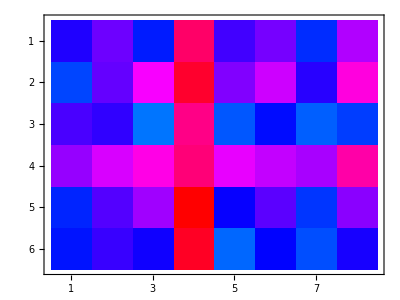

```mathematica
MatrixPlot[rrmse[[o]]ᵀ,ColorFunction->Hue]
```

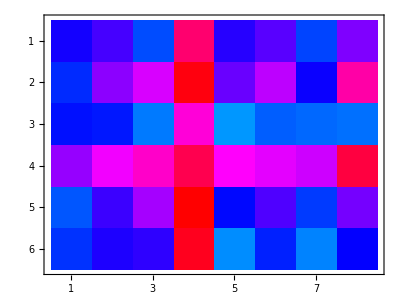

```mathematica
MatrixPlot[rdsv[[o]]ᵀ,ColorFunction->Hue]
```

```mathematica
measures
```

{Variance,VaR 99%,VaR 95%,ES 99%,ES 95%,Spectral 10}

```mathematica
ticks1 = Table[{ii,measures[[ii]]}, {ii, 1, Length[measures]}];
ticks2 = Table[{ii,copulas[[o[[ii]]]]}, {ii, 1, Length[o]}];
```

Unfortunately, the plot below does not plot the whole data

```mathematica
ListPlot3D[rrmse[[o]]ᵀ,Mesh->None,InterpolationOrder->0,ColorFunction->"Rainbow",Ticks->{ticks2, ticks1},ViewPoint->{-2.5, -3, 1}]
```

-Graphics3D-

```mathematica
{Min[rrmse[[o]]],Max[rrmse[[o]]]}
```

{0.156749,0.461462}

```mathematica
ArrayPlot[rrmse[[o]],ColorFunction->"Rainbow",FrameTicks->{{ticks2,None},{ticks1,None}},ColorFunctionScaling->True,PlotRange->{Min[rrmse[[o]]], Max[rrmse[[o]]]},PlotLegends->Automatic]
```

-Graphics-

```mathematica
ArrayPlot[rdsv[[o]],ColorFunction->"Rainbow",FrameTicks->{{ticks2,None},{ticks1,None}},ColorFunctionScaling->True,PlotRange->{Min[rdsv[[o]]], Max[rdsv[[o]]]},PlotLegends->Automatic]
```

-Graphics-

```mathematica
MinMax[rrmse[[o]]]
```

{0.156749,0.461462}

```mathematica
p1=ArrayPlot[Log[rrmse[[o]]],FrameTicks->{{ticks2,None},{ticks1,None}},ColorFunction->"Rainbow",ColorFunctionScaling->True, FrameTicksStyle->Directive[Black, 12, FontFamily->"Times"],PlotLegends->Placed[BarLegend[{(ColorData["Rainbow"][Rescale[#,MinMax[rrmse[[o]]]]]&),MinMax[rrmse[[o]]]},LegendMarkerSize->500,LabelStyle->Directive[Black,12,FontFamily->"Times"]],{1.,0.5}]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<> "../latex/_pics/rrmse_static.pdf", p1]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/rrmse_static.pdf

```mathematica
p1=ArrayPlot[Log[rdsv[[o]]],FrameTicks->{{ticks2,None},{ticks1,None}},ColorFunction->"Rainbow",ColorFunctionScaling->True, FrameTicksStyle->Directive[Black, 12, FontFamily->"Times"],PlotLegends->Placed[BarLegend[{(ColorData["Rainbow"][Rescale[#,MinMax[rdsv[[o]]]]]&),MinMax[rdsv[[o]]]},LegendMarkerSize->500,LabelStyle->Directive[Black,12,FontFamily->"Times"]],{1.,0.5}]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<> "../latex/_pics/rdsv_static.pdf", p1]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/rdsv_static.pdf

```mathematica
p={};
For[ii=1, ii<=Length[copulas], ii++,
AppendTo[p, BoxWhiskerChart[dFull[[ii,2;;]]ᵀ, ChartLabels->dFull[[ii,1]],PlotRange->{Automatic,{0.6,1.5}},PlotTheme->"Classic", PlotLabel->copulas[[ii]]]];
]
```

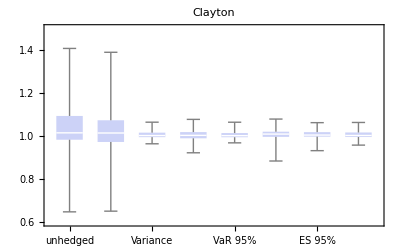
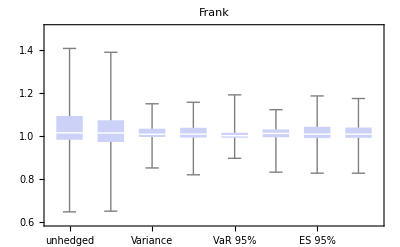
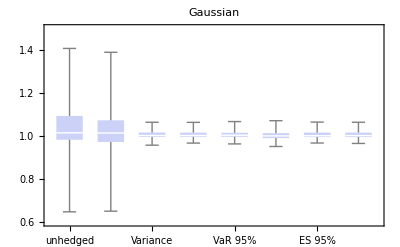
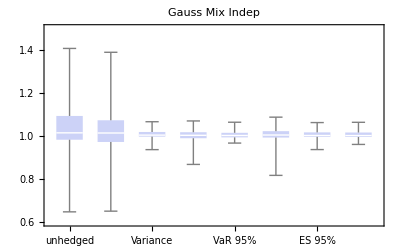
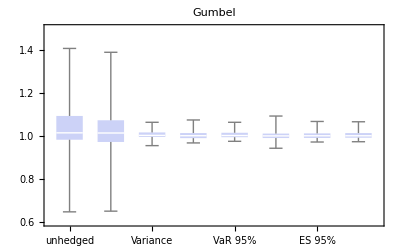
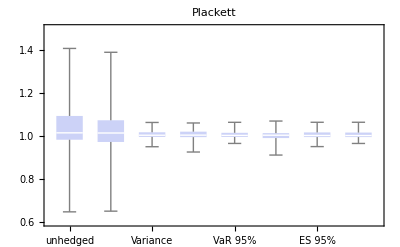
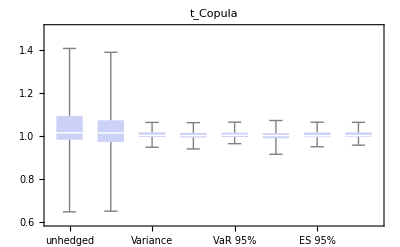
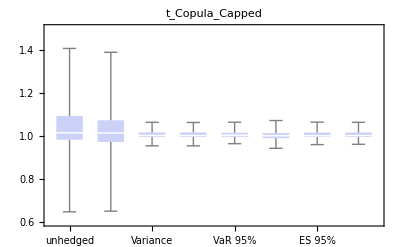

```mathematica
p
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/PL_static_out_tcop.pdf",p[[7]]];
```

```mathematica
p={};
For[ii=1, ii<=Length[copulas], ii++,
AppendTo[p,  BoxWhiskerChart[dFull⟦ii,2;;All,3;;All⟧ᵀ, (*ChartLabels->dFull[[ii,1,3;;]],*)PlotRange->{Automatic,{0.8,1.2}},PlotTheme->"Classic", PlotLabel->copulas⟦ii⟧]];
]
```

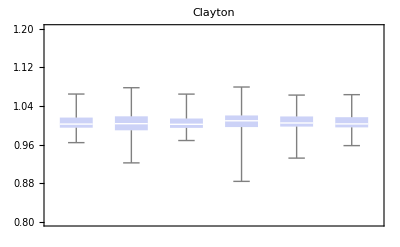
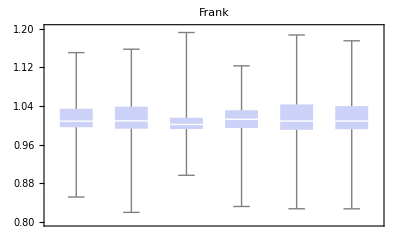
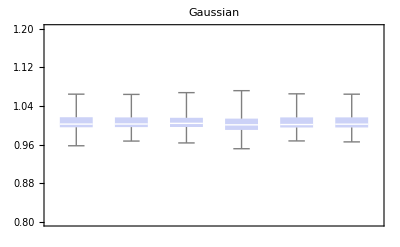
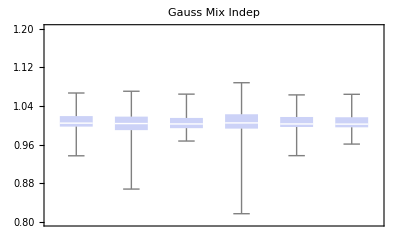
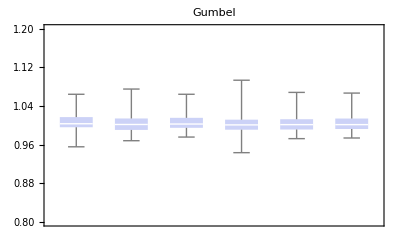
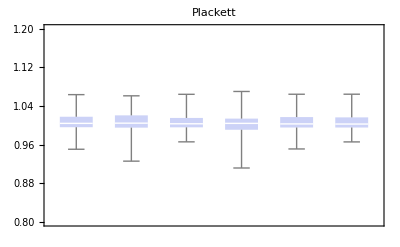
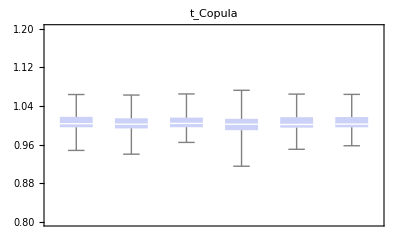
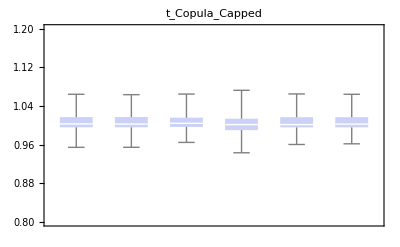

```mathematica
p
```

```mathematica
Export[NotebookDirectory[]<> "../latex/_pics/PL_static_out.pdf", Grid[{{p⟦3⟧,p⟦7⟧,p⟦1⟧,p⟦2⟧},{p⟦5⟧,p⟦6⟧,p⟦9⟧,p⟦4⟧}}]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/PL_static_out.pdf

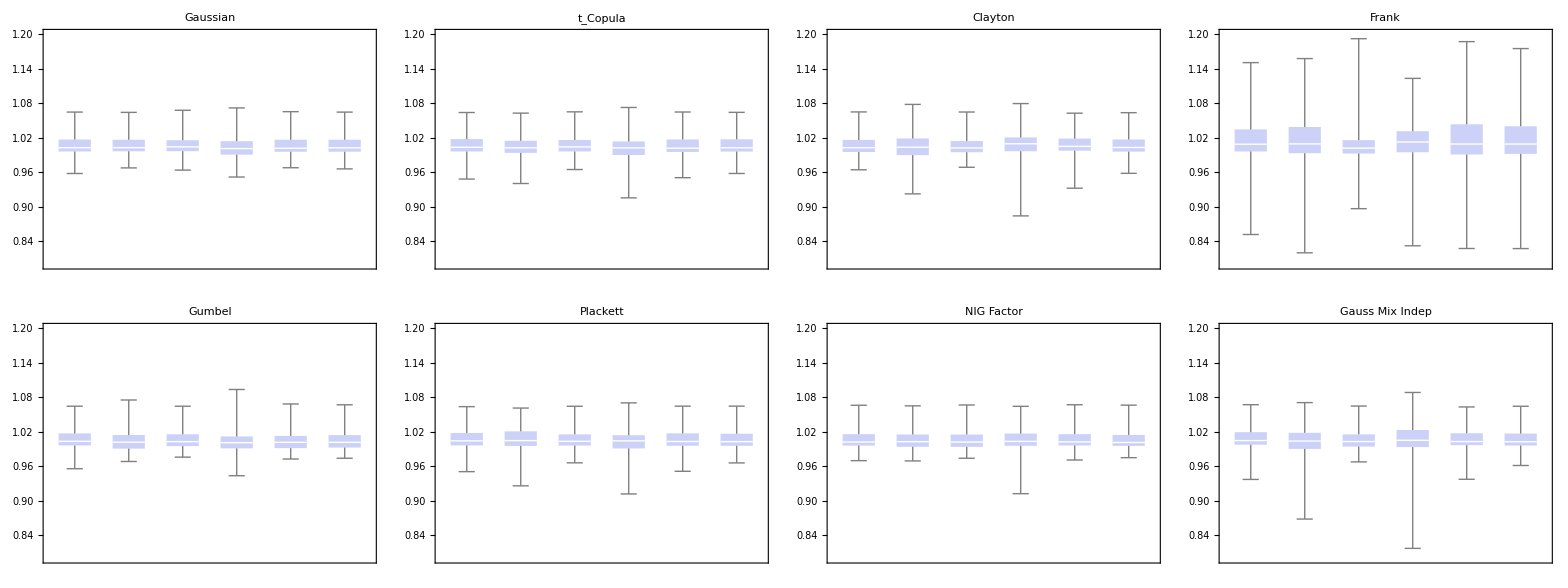

```mathematica
Grid[{{p⟦3⟧,p⟦7⟧,p⟦1⟧,p⟦2⟧},{p⟦5⟧,p⟦6⟧,p⟦9⟧,p⟦4⟧}}]
```

#### Out-of-sample (dynamic)

Uses 5 days of out-of-sample data

```mathematica
dFull={};
For[ii=1, ii≤Length[copulas],ii++,
d={};
For[kk=0, kk≤87, kk++,
d1=Import[NotebookDirectory[] <> "data_PL_5Days/" <> ToString[kk] <> "_" <> copulas[[ii]]<> "_PLr_outsample.csv"];
If[kk==0,
d=Join[d, d1],
d=Join[d,d1[[2;;]]]
];
];
AppendTo[dFull, d];
]
```

```mathematica
Dimensions[dFull]
```

{9,441,9}

```mathematica
copulas
```

{Clayton,Frank,Gaussian,Gauss Mix Indep,Gumbel,Plackett,t_Copula,t_Copula_Capped,NIG Factor}

```mathematica
measures=d1[[1,2;;]]
```

{unhedged,future,Variance,VaR 99%,VaR 95%,ES 99%,ES 95%,Spectral 10}

```mathematica
dFull[[1,-10;;]]//TableForm
```

2019-09-05 | -0.016273 | -0.0181211 | 0.000245281 | -0.00172734 | 0.00142454 | -0.00394152 | -0.00107756 | 0.0000313591
2019-09-04 | 0.00471983 | 0.0129771 | -0.00721373 | -0.00577067 | -0.00807876 | -0.00415676 | -0.00624547 | -0.007057
2019-09-03 | 0.095907 | 0.113016 | -0.00855983 | 0.00459949 | -0.0165227 | 0.0191366 | 0.000286773 | -0.0071231
2019-08-30 | 0.00172564 | 0.00551219 | -0.00332214 | -0.00271359 | -0.00368669 | -0.00203239 | -0.00291387 | -0.00325607
2019-08-29 | -0.0189245 | -0.0203616 | -0.00035451 | -0.00257016 | 0.000969772 | -0.00505776 | -0.00184026 | -0.000594761
2019-08-28 | 0.0101389 | 0.00634613 | 0.00433139 | 0.00503744 | 0.00387444 | 0.00581594 | 0.0048104 | 0.00441433
2019-08-27 | 0.0207079 | 0.0264121 | -0.00367496 | -0.000686251 | -0.00561283 | 0.00260121 | -0.00164659 | -0.0033235
2019-08-26 | -0.0116521 | -0.00761184 | -0.00462759 | -0.0054768 | -0.0040787 | -0.00641468 | -0.00520358 | -0.00472728
2019-08-23 | -0.0128616 | -0.0163701 | 0.00213765 | 0.000330677 | 0.00330467 | -0.00166697 | 0.000912242 | 0.00192561
2019-08-22 | -0.0539532 | -0.0553896 | -0.00301738 | -0.00905774 | 0.000870187 | -0.0157654 | -0.00711089 | -0.00372488

```mathematica
measures
```

{unhedged,future,Variance,VaR 99%,VaR 95%,ES 99%,ES 95%,Spectral 10}

```mathematica
Length[measures]
```

8

```mathematica
rmse=Table[RootMeanSquare[dFull[[kk,2;;,ii]]], {ii,4,Length[measures]+1}, {kk, 1,Length[copulas]}];
dsv = Table[RootMeanSquare[Min[#,0]&/@dFull[[kk,2;;,ii]]], {ii,4,Length[measures]+1}, {kk, 1,Length[copulas]}];
rmseUnhedged=RootMeanSquare[dFull[[1,2;;,2]]];
dsvUnhedged=RootMeanSquare[Min[#,0]&/@dFull[[1,2;;,2]]];
rrmse=rmse/rmseUnhedged;
rdsv = dsv/dsvUnhedged;
```

```mathematica
rrmse
```

(0.20144 | 0.364429 | 0.201546 | 0.214172 | 0.202273 | 0.207065 | 0.204994 | 0.202461 | 0.199441
0.228604 | 0.426339 | 0.207858 | 0.261068 | 0.233188 | 0.219854 | 0.215854 | 0.212447 | 0.210313
0.20284 | 0.337499 | 0.210991 | 0.202918 | 0.201107 | 0.206395 | 0.206234 | 0.208592 | 0.19848
0.268089 | 0.353701 | 0.219212 | 0.313617 | 0.268253 | 0.224052 | 0.229915 | 0.221233 | 0.211529
0.215906 | 0.459901 | 0.201952 | 0.208712 | 0.214108 | 0.205724 | 0.205429 | 0.203176 | 0.199014
0.20413 | 0.427284 | 0.20268 | 0.203029 | 0.202367 | 0.20388 | 0.204079 | 0.203185 | 0.197671)

```mathematica
rdsv
```

(0.178344 | 0.358879 | 0.176418 | 0.191826 | 0.175804 | 0.180143 | 0.181411 | 0.177777 | 0.172787
0.221466 | 0.422757 | 0.175654 | 0.260949 | 0.228312 | 0.199437 | 0.195798 | 0.184617 | 0.190072
0.174325 | 0.32823 | 0.182647 | 0.173189 | 0.175195 | 0.176829 | 0.174894 | 0.179249 | 0.173053
0.261408 | 0.356284 | 0.209922 | 0.329972 | 0.275138 | 0.21762 | 0.227593 | 0.213778 | 0.185245
0.18853 | 0.452759 | 0.176647 | 0.186537 | 0.201331 | 0.178898 | 0.182874 | 0.17904 | 0.174518
0.176939 | 0.425177 | 0.176526 | 0.176584 | 0.181975 | 0.176346 | 0.178756 | 0.177391 | 0.171897)

```mathematica
measures
```

{unhedged,future,Variance,VaR 99%,VaR 95%,ES 99%,ES 95%,Spectral 10}

```mathematica
o
```

{3,7,1,2,5,6,9,4}

```mathematica
rrmse=rrmseᵀ;
rdsv=rdsvᵀ;
```

```mathematica
Prepend[Prepend[rrmse[[o]]ᵀ,copulas[[o]]]ᵀ,Flatten[Join[{""},measures[[3;;]]]]]//TableForm
```

| Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
Gaussian | 0.201546 | 0.207858 | 0.210991 | 0.219212 | 0.201952 | 0.20268
t_Copula | 0.204994 | 0.215854 | 0.206234 | 0.229915 | 0.205429 | 0.204079
Clayton | 0.20144 | 0.228604 | 0.20284 | 0.268089 | 0.215906 | 0.20413
Frank | 0.364429 | 0.426339 | 0.337499 | 0.353701 | 0.459901 | 0.427284
Gumbel | 0.202273 | 0.233188 | 0.201107 | 0.268253 | 0.214108 | 0.202367
Plackett | 0.207065 | 0.219854 | 0.206395 | 0.224052 | 0.205724 | 0.20388
NIG Factor | 0.199441 | 0.210313 | 0.19848 | 0.211529 | 0.199014 | 0.197671
Gauss Mix Indep | 0.214172 | 0.261068 | 0.202918 | 0.313617 | 0.208712 | 0.203029

```mathematica
Prepend[Prepend[rdsv[[o]]ᵀ,copulas[[o]]]ᵀ,Flatten[Join[{""},measures[[3;;]]]]]//TableForm
```

| Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
Gaussian | 0.176418 | 0.175654 | 0.182647 | 0.209922 | 0.176647 | 0.176526
t_Copula | 0.181411 | 0.195798 | 0.174894 | 0.227593 | 0.182874 | 0.178756
Clayton | 0.178344 | 0.221466 | 0.174325 | 0.261408 | 0.18853 | 0.176939
Frank | 0.358879 | 0.422757 | 0.32823 | 0.356284 | 0.452759 | 0.425177
Gumbel | 0.175804 | 0.228312 | 0.175195 | 0.275138 | 0.201331 | 0.181975
Plackett | 0.180143 | 0.199437 | 0.176829 | 0.21762 | 0.178898 | 0.176346
NIG Factor | 0.172787 | 0.190072 | 0.173053 | 0.185245 | 0.174518 | 0.171897
Gauss Mix Indep | 0.191826 | 0.260949 | 0.173189 | 0.329972 | 0.186537 | 0.176584

```mathematica
MinMax[rrmse[[o]]]
```

{0.197671,0.459901}

```mathematica
Log[2,MinMax[rrmse[[o]]]]
```

{-2.33883,-1.1206}

```mathematica
p1=ArrayPlot[Log[rrmse[[o]]],FrameTicks->{{ticks2,None},{ticks1,None}},ColorFunction->"Rainbow",ColorFunctionScaling->True, FrameTicksStyle->Directive[Black, 12, FontFamily->"Times"],
PlotLegends->Placed[BarLegend[{(ColorData["Rainbow"][Rescale[#,MinMax[rrmse[[o]]]]]&),MinMax[rrmse[[o]]]},LegendMarkerSize->500,LabelStyle->Directive[Black,15,FontFamily->"Times"]],{1.,0.5}]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<> "../latex/_pics/rrmse_dynamic.pdf", p1]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/rrmse_dynamic.pdf

```mathematica
p1=ArrayPlot[Log[rdsv[[o]]],FrameTicks->{{ticks2,None},{ticks1,None}},ColorFunction->"Rainbow",ColorFunctionScaling->True, FrameTicksStyle->Directive[Black, 12, FontFamily->"Times"],
PlotLegends->Placed[BarLegend[{(ColorData["Rainbow"][Rescale[#,MinMax[rdsv[[o]]]]]&),MinMax[rdsv[[o]]]},LegendMarkerSize->500,LabelStyle->Directive[Black,15,FontFamily->"Times"]],{1.,0.5}]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<> "../latex/_pics/rdsv_dynamic.pdf", p1]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/rdsv_dynamic.pdf

```mathematica
p={};
For[ii=1, ii<=Length[copulas], ii++,
AppendTo[p, BoxWhiskerChart[dFull[[ii,2;;,2;;]]ᵀ, ChartLabels->dFull[[ii,1,2;;]],PlotRange->{Automatic,Full},PlotTheme->"Classic", PlotLabel->copulas[[ii]]]];
]
```

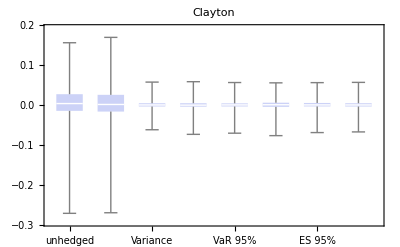
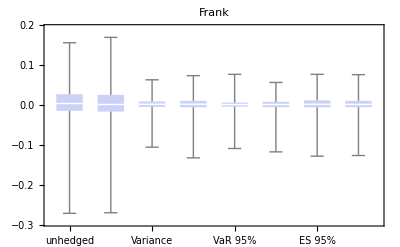
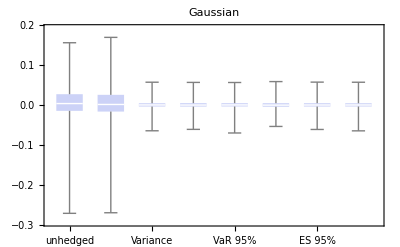
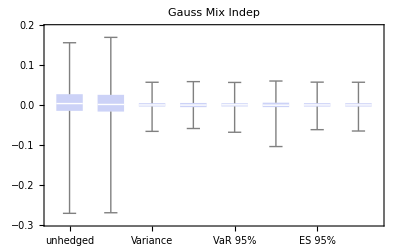
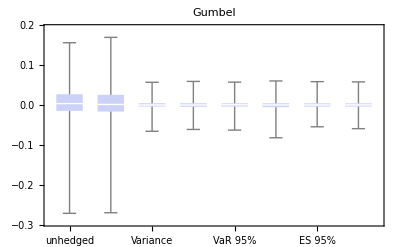
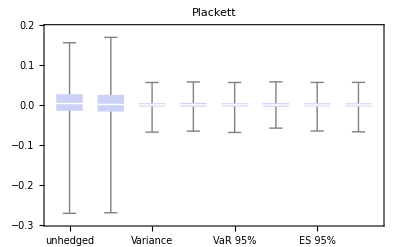
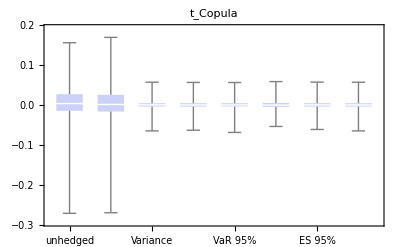
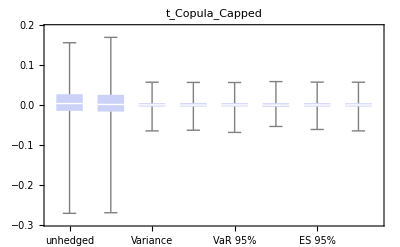

```mathematica
p
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/PL_dynamic_out_tcop.pdf",p[[7]]];
```

```mathematica
p[[7]]
```

-Graphics-

```mathematica
p={};
For[ii=1, ii<=Length[copulas], ii++,
AppendTo[p,  BoxWhiskerChart[dFull⟦ii,2;;All,4;;All⟧ᵀ, (*ChartLabels->dFull[[ii,1,3;;]],*)PlotRange->{Automatic,{-0.15,0.15}},PlotTheme->"Classic", PlotLabel->copulas⟦ii⟧]];
]
```

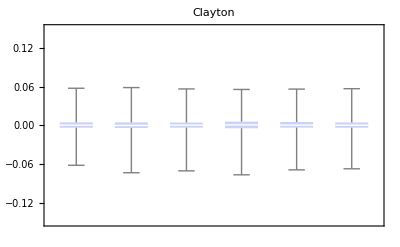
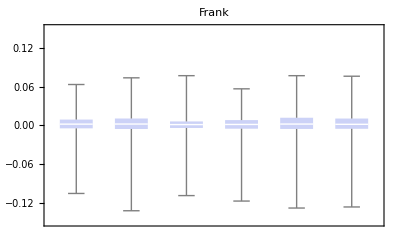
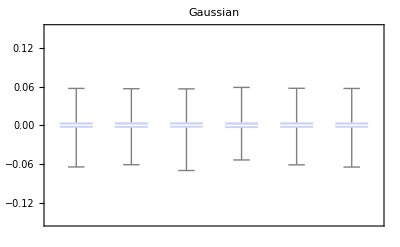
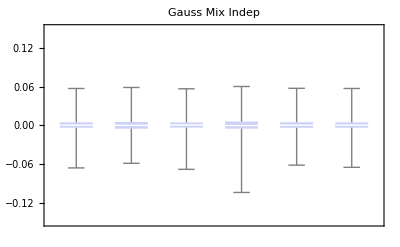
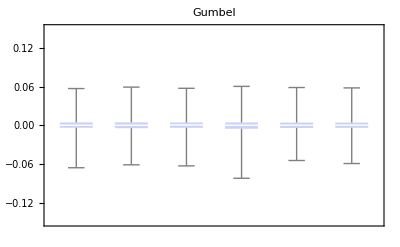
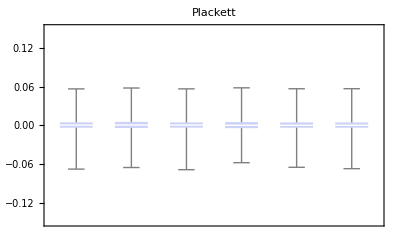
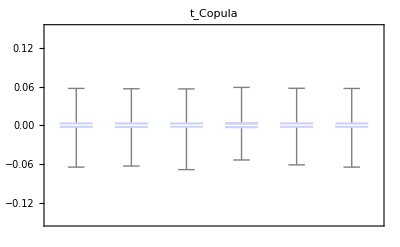
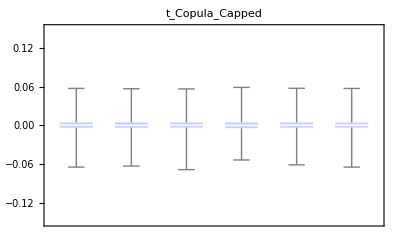

```mathematica
p
```

```mathematica
Export[NotebookDirectory[]<> "../latex/_pics/PL_dynamic_out.pdf", Grid[{{p⟦3⟧,p⟦7⟧,p⟦1⟧,p⟦2⟧},{p⟦5⟧,p⟦6⟧,p⟦9⟧,p⟦4⟧}}]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/PL_dynamic_out.pdf

```mathematica
Dimensions[dFull]
```

{9,441,9}

```mathematica
dFull[[2, 1;;10]]
```

(Date | unhedged | future | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
2021-05-27 | -0.131176 | -0.108809 | -0.0494437 | -0.0521236 | -0.0750622 | -0.0407648 | -0.0643213 | -0.0572705
2021-05-26 | 0.0932707 | 0.09433 | 0.025754 | 0.0281331 | 0.0480151 | 0.017966 | 0.0388114 | 0.0326687
2021-05-25 | -0.0576258 | -0.0622446 | -0.0123507 | -0.0138614 | -0.0267193 | -0.00744636 | -0.0207148 | -0.0167577
2021-05-24 | 0.0540123 | 0.0326431 | 0.0309724 | 0.0317669 | 0.0384558 | 0.0283804 | 0.0353485 | 0.0332851
2021-05-21 | 0.00557281 | 0.00658279 | 0.000803005 | 0.000966038 | 0.00234271 | 0.000271834 | 0.00170226 | 0.00127785
2021-05-20 | 0.0547603 | 0.03685 | 0.0291817 | 0.0306546 | 0.0371888 | 0.0273215 | 0.034292 | 0.0322318
2021-05-19 | -0.123533 | -0.131645 | -0.0289671 | -0.0341138 | -0.057365 | -0.0225153 | -0.0469713 | -0.039663
2021-05-18 | -0.0120673 | -0.0196938 | 0.00186183 | 0.00107456 | -0.00243957 | 0.00285359 | -0.000877267 | 0.000229552
2021-05-17 | -0.157294 | -0.0904653 | -0.0878266 | -0.0916518 | -0.10887 | -0.0830242 | -0.101186 | -0.0957706)

```mathematica
d=dFull⟦1⟧;
```

```mathematica
dates=Table[DateList[{d⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[d⟦2;;All,1⟧]}];
```

```mathematica
extremes=Sort[Abs[d[[2;;,2]]]][[-20;;]];
pos=Flatten[Table[Position[Abs[d[[;;,2]]],extremes[[k]]], {k,1,Length[extremes]}]];
```

```mathematica
pos
```

{297,126,16,269,117,99,209,8,69,257,2,392,81,105,94,301,10,419,303,306}

```mathematica
p1=DateListPlot[{dates,d[[2;;,2]]}ᵀ,PlotRange->{-0.3,0.25},PlotTheme->"Classic",Joined->True,PlotStyle->Thick,AspectRatio->1/4,PlotRange->Full,PlotLabel->"Bitcoin spot"];
```

```mathematica
p1a=DateListPlot[Transpose[{dates⟦pos-1⟧,d[[pos,2]]}],PlotStyle->{Red,Thick},Joined->False];
```

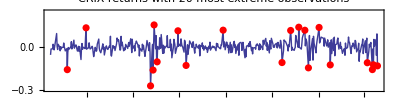

```mathematica
p1b=Show[p1,p1a, PlotLabel->"CRIX returns with 20 most extreme observations",AspectRatio->1/4]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/BTCspot_with_extremes.pdf", p1b];
```

```mathematica
p2=DateListPlot[{dates,d[[2;;,3]]}ᵀ,PlotRange->{-0.3,0.25},PlotTheme->"Classic",Joined->True,PlotStyle->Thick,AspectRatio->1/4,PlotRange->Full,PlotLabel->"Bitcoin future"];
```

```mathematica
p2a=DateListPlot[Transpose[{dates⟦pos-1⟧,d⟦pos,3⟧}],PlotStyle->{Red,Thick},Joined->False];
```

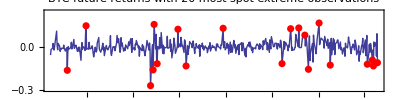

```mathematica
p2b=Show[p2,p2a, PlotLabel->"BTC future returns with 20 most spot extreme observations",AspectRatio->1/4]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/BTCfuture_with_extremes.pdf", p2b];
```

```mathematica
For[kk=1, kk≤Length[copulas], kk++,
d=dFull⟦kk⟧;
p=Table[Show[
DateListPlot[{dates,d⟦2;;All,m⟧}ᵀ,PlotRange->{-0.25,0.25},PlotLabel->methods⟦m-3⟧,PlotTheme->"Classic",Joined->True,PlotStyle->Thick(*,AspectRatio->1/4*)],
DateListPlot[Transpose[{dates⟦pos-1⟧,d⟦pos,m⟧}],PlotStyle->{Red,Thick},Joined->False]
],
 {m,4,9}];
Export[NotebookDirectory[] <> "../latex/_pics/PL_dyn_series_"<> copulas⟦kk⟧ <> ".pdf",Grid[{{p⟦1⟧,p⟦2⟧,p⟦3⟧},{p⟦4⟧,p⟦5⟧,p⟦6⟧},{"",copulas⟦kk⟧}}]];
]
```

```mathematica
Dimensions[dFull]
```

{9,441,9}